Seth AbuHamdeh

Problem 2a: mywager3

Problem 2b:myWager5

Problem 2c:myWager4

Problem 2d: myWager1

Problem 2e: myWager2

```mathematica
initializeMoney:=(totalMoney=10);
```

```mathematica
returnedMoney[w_]:=Module[{x},(x=RandomVariate[NormalDistribution[1.1,1]];If[x<0,x=0];If[(1<x)&&(x<1.7),x=1.1];w*x)]
```

```mathematica
investStep[tot_]:=If[(tot<.01)||(tot<myWager[tot]),0,tot-myWager[tot]+returnedMoney[myWager[tot]]]
```

Problem 3

```mathematica
Clear[myWager];
myWager[totalMoney_]:=Piecewise[{{.25*totalMoney, totalMoney < 40}, {.2, totalMoney  >=40}}];
```

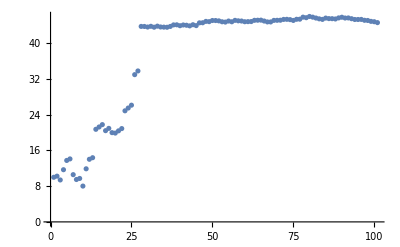

```mathematica
initializeMoney;
accountBalances=NestList[investStep,totalMoney,100];
ListPlot[accountBalances]
```

```mathematica
f[] := (initializeMoney;
accountBalances = NestList[investStep,totalMoney, 100];
accountBalances[[-1]])
mytable = Table[f[],{i,1,1000}];
Median[mytable]
```

41.6398

25.3441

24.0483